```mathematica
CC=Import["D://Mathematica//bbs.xls"]
```

{{{1.,1.,1.,winson,2.,test,1.2422×10^9},{2.,2.,1.,jzhu,3.,Maze: transition probability,1.24221×10^9},{4.,2.,0.,winson,2.,,1.24236×10^9},{6.,2.,0.,zhanglun,7.,,1.24241×10^9},«2972»,{3180.,762.,0.,Qinjie,25.,å›žå¤.8d 1# è®¡ç®—å£« çš„å.b8–å.90,1.2892×10^9},{3177.,763.,1.,è®¡ç®—å£«,11.,comments on ã€Šç¤.beä.bcšç‰©ç.90†å.a6ï.bcšç.90†è®.baä.b8Žå.ba”ç”.a8ã€‹,1.28916×10^9},{3182.,764.,1.,winson,2.,Graphical Models for Time Series,1.28939×10^9},{3185.,765.,1.,jzhu,3.,201010 data have been uploaded,1.2896×10^9}}}

```mathematica
DD=CC[[1]]
```

{{1.,1.,1.,winson,2.,test,1.2422×10^9},{2.,2.,1.,jzhu,3.,Maze: transition probability,1.24221×10^9},{4.,2.,0.,winson,2.,,1.24236×10^9},{6.,2.,0.,zhanglun,7.,,1.24241×10^9},{7.,2.,0.,winson,2.,,1.24245×10^9},«2971»,{3180.,762.,0.,Qinjie,25.,å›žå¤.8d 1# è®¡ç®—å£« çš„å.b8–å.90,1.2892×10^9},{3177.,763.,1.,è®¡ç®—å£«,11.,comments on ã€Šç¤.beä.bcšç‰©ç.90†å.a6ï.bcšç.90†è®.baä.b8Žå.ba”ç”.a8ã€‹,1.28916×10^9},{3182.,764.,1.,winson,2.,Graphical Models for Time Series,1.28939×10^9},{3185.,765.,1.,jzhu,3.,201010 data have been uploaded,1.2896×10^9}}

```mathematica
Tally[Transpose[DD][[4]]]//MatrixForm
```

(winson | 355
jzhu | 806
zhanglun | 546
luheng | 277
admin | 6
xiangly | 82
è®¡ç®—å£« | 258
zhijin | 12
linbo | 9
zhenzhen | 41
LiangHai | 238
Chengjun | 43
jiangping | 12
shaojsun | 34
xzzhang2 | 41
yingli9 | 32
zxiong2 | 30
yanyi3 | 39
zhanghua | 9
sdx061 | 27
wooder58 | 38
Qinjie | 41
Tianjiao | 4)

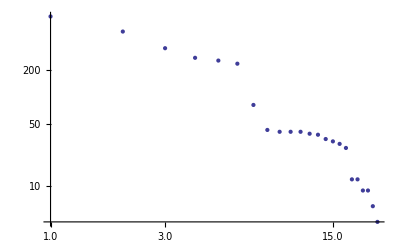

```mathematica
ListLogLogPlot[Sort[Transpose[Tally[Transpose[DD][[4]]]][[2]],Greater]]
```

```mathematica
tt=Union[Transpose[DD][[1]]];
```

```mathematica
E={{3,2},{3,4}}
```

Set::wrsym: Symbol ⅇ is Protected.

{{3,2},{3,4}}

```mathematica
First[CC]//TableForm;
```

```mathematica
{1.,1.,"winson",2.}[[1]]==1
```

True

```mathematica
thread[n_]:=Select[DD,#[[1]]==n&]
```

```mathematica
k=thread[2]
```

{{2.,2.,1.,jzhu,3.,Maze: transition probability,1.24221×10^9}}

```mathematica
First[k][[3]]
```

1.

```mathematica
Transpose[Drop[k,1]][[3]]
```

Transpose::nmtx: The first two levels of the one-dimensional list {} cannot be transposed.

Part::partw: Part 3 of Transpose[{}] does not exist.

Transpose[{}]⟦3⟧

```mathematica
Transpose[{}]⟦3⟧
```

Transpose::nmtx: The first two levels of the one-dimensional list {} cannot be transposed.

Part::partw: Part 3 of Transpose[{}] does not exist.

```mathematica
Transpose[{}]⟦3⟧
```

Transpose::nmtx: The first two levels of the one-dimensional list {} cannot be transposed.

Part::partw: Part 3 of Transpose[{}] does not exist.

Transpose[{}]⟦3⟧

```mathematica
Rule[#,First[k][[3]]]&/@Transpose[Drop[k,1]][[3]]
```

Transpose::nmtx: The first two levels of the one-dimensional list {} cannot be transposed.

Part::partw: Part 3 of Transpose[{}] does not exist.

Part::pspec: Part specification 3 → 1.` is neither an integer nor a list of integers.

(Transpose[{}]→1.)⟦3→1.⟧

```mathematica
Length[{}]
```

0

```mathematica
If
```

```mathematica
net[m_]:=Module[{thread},
thread=Select[DD,#[[1]]==m&];
If[Length[thread]>1,
Rule[#,First[thread][[3]]]&/@Transpose[Drop[thread,1]][[3]],0]
]
```

```mathematica
Length["Chengjun"->"Chengjun"]
```

2

```mathematica
Text[Style["aa",Large]]
```

aa

```mathematica
bbs=Select[Sort[Flatten[net[#]&/@tt]],Length[#]>1&]
```

{}

```mathematica
Tally[bbs]
```

{{admin→admin,1},{admin→luheng,1},{admin→zhanglun,1},{Chengjun→Chengjun,10},{Chengjun→jzhu,3},{Chengjun→LiangHai,2},{Chengjun→lingfei,6},{Chengjun→luheng,2},{Chengjun→Qinjie,1},{Chengjun→xiangly,1},{Chengjun→zhanglun,1},{jiangping→jzhu,6},{jiangping→lingfei,1},{jzhu→admin,5},{jzhu→Chengjun,8},{jzhu→jzhu,265},{jzhu→LiangHai,48},{jzhu→linbo,4},{jzhu→lingfei,32},{jzhu→luheng,61},{jzhu→Qinjie,4},{jzhu→sdx061,4},{jzhu→shaojsun,18},{jzhu→winson,50},{jzhu→wooder58,4},{jzhu→xiangly,33},{jzhu→xzzhang2,13},{jzhu→zhanglun,118},{jzhu→zhenzhen,5},{jzhu→zhijin,1},{LiangHai→Chengjun,1},{LiangHai→jzhu,63},{LiangHai→LiangHai,31},{LiangHai→lingfei,13},{LiangHai→luheng,20},{LiangHai→Qinjie,1},{LiangHai→winson,10},{LiangHai→wooder58,1},{LiangHai→xiangly,2},{LiangHai→xzzhang2,7},{LiangHai→zhanglun,9},{linbo→admin,1},{linbo→jzhu,1},{linbo→linbo,1},{lingfei→Chengjun,1},{lingfei→jzhu,56},{lingfei→LiangHai,11},{lingfei→lingfei,55},{lingfei→luheng,13},{lingfei→winson,5},{lingfei→xiangly,2},{lingfei→xzzhang2,4},{lingfei→zhanglun,46},{luheng→admin,4},{luheng→jzhu,88},{luheng→LiangHai,9},{luheng→lingfei,3},{luheng→luheng,27},{luheng→sdx061,1},{luheng→shaojsun,5},{luheng→winson,9},{luheng→xiangly,2},{luheng→xzzhang2,5},{luheng→zhanglun,39},{luheng→zhijin,1},{Qinjie→jzhu,6},{Qinjie→lingfei,1},{Qinjie→luheng,8},{Qinjie→Qinjie,6},{Qinjie→winson,1},{Qinjie→xiangly,1},{Qinjie→zhanglun,1},{Qinjie→zhenzhen,2},{sdx061→jzhu,6},{sdx061→sdx061,15},{sdx061→wooder58,2},{sdx061→xiangly,1},{shaojsun→jzhu,1},{shaojsun→shaojsun,29},{shaojsun→xiangly,1},{Tianjiao→luheng,4},{winson→admin,4},{winson→Chengjun,1},{winson→jzhu,93},{winson→LiangHai,19},{winson→linbo,3},{winson→lingfei,17},{winson→luheng,29},{winson→Qinjie,3},{winson→sdx061,3},{winson→shaojsun,11},{winson→winson,59},{winson→wooder58,1},{winson→xiangly,1},{winson→zhanglun,38},{winson→zhijin,2},{wooder58→jzhu,34},{wooder58→xiangly,1},{xiangly→jzhu,6},{xiangly→luheng,3},{xiangly→winson,4},{xiangly→xiangly,18},{xiangly→zhanglun,4},{xzzhang2→jzhu,27},{xzzhang2→xzzhang2,7},{xzzhang2→zxiong2,1},{yanyi3→jzhu,32},{yanyi3→LiangHai,2},{yanyi3→xzzhang2,5},{yingli9→jiangping,1},{yingli9→jzhu,25},{yingli9→LiangHai,1},{yingli9→xzzhang2,5},{zhanghua→jzhu,8},{zhanghua→LiangHai,1},{zhanglun→admin,10},{zhanglun→Chengjun,1},{zhanglun→jzhu,129},{zhanglun→LiangHai,19},{zhanglun→linbo,1},{zhanglun→lingfei,5},{zhanglun→luheng,18},{zhanglun→Qinjie,1},{zhanglun→winson,20},{zhanglun→wooder58,1},{zhanglun→xiangly,2},{zhanglun→xzzhang2,4},{zhanglun→zhanglun,202},{zhanglun→zhijin,1},{zhenzhen→jzhu,10},{zhenzhen→LiangHai,4},{zhenzhen→lingfei,1},{zhenzhen→luheng,2},{zhenzhen→winson,1},{zhenzhen→xiangly,1},{zhenzhen→xzzhang2,1},{zhenzhen→zhanglun,2},{zhenzhen→zhenzhen,6},{zhijin→jzhu,3},{zhijin→winson,1},{zhijin→zhanglun,2},{zhijin→zhijin,1},{zxiong2→jzhu,23},{zxiong2→LiangHai,1},{zxiong2→xzzhang2,5}}

```mathematica
fre=Sort[Transpose[Tally[bbs]][[2]],Greater]
```

{265,202,129,118,93,88,63,61,59,56,55,50,48,46,39,38,34,33,32,32,31,29,29,27,27,25,23,20,20,19,19,18,18,18,17,15,13,13,13,11,11,10,10,10,10,9,9,9,8,8,8,7,7,6,6,6,6,6,6,6,5,5,5,5,5,5,5,5,5,4,4,4,4,4,4,4,4,4,4,4,4,3,3,3,3,3,3,3,2,2,2,2,2,2,2,2,2,2,2,2,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

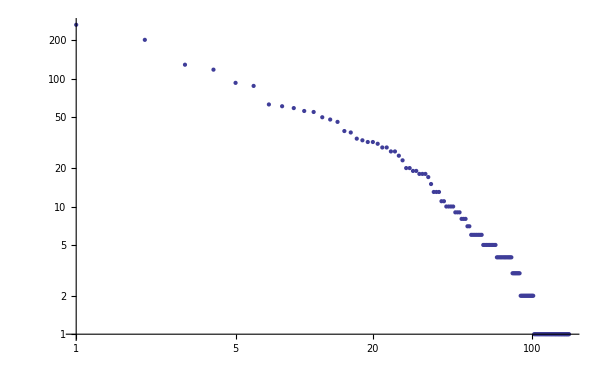

```mathematica
ListLogLogPlot[fre,PlotRange->All]
```

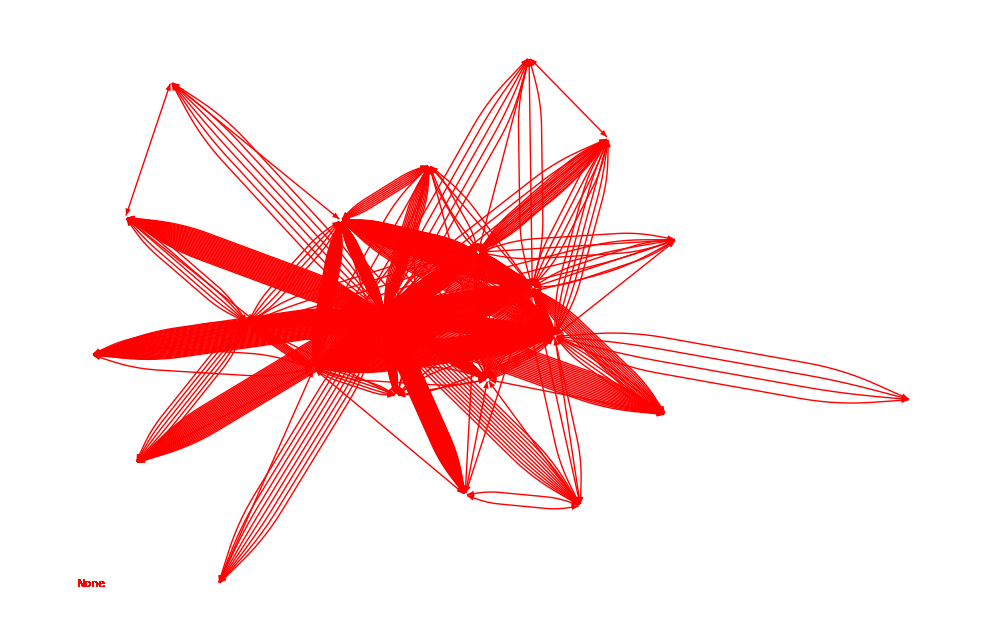

```mathematica
GraphPlot[bbs,SelfLoopStyle->None,ImageSize->1000,
EdgeRenderingFunction->({Red,Text[#3],Arrowheads[{-.01,.01}],Arrow[#1,0.01]}&),
VertexRenderingFunction->({Blue,Text[Style[#2,20,Bold],#1]}&)]
```

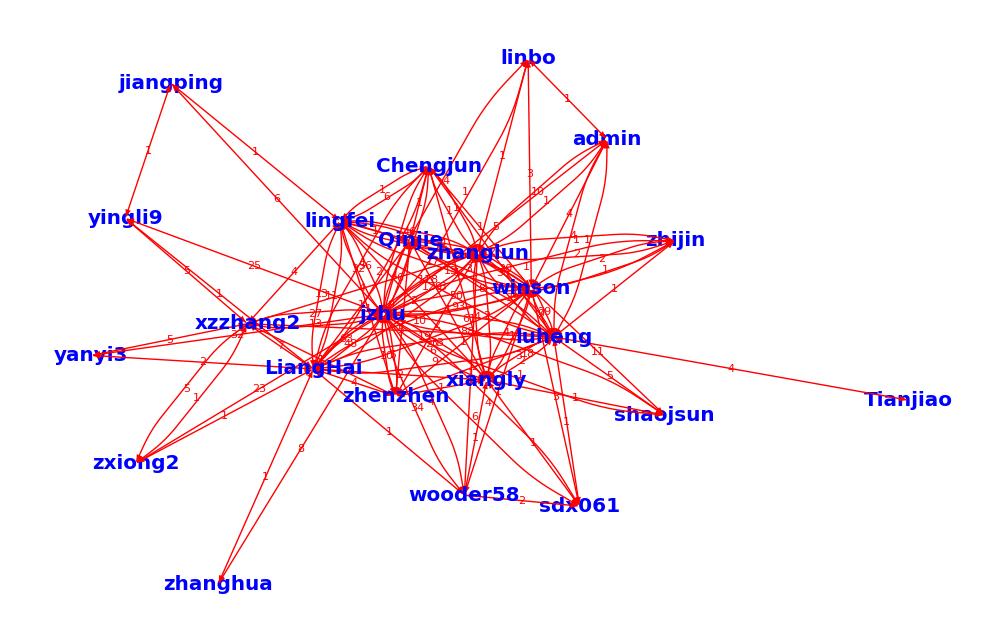

```mathematica
GraphPlot[Tally[bbs],ImageSize->1000,SelfLoopStyle->None,VertexLabeling->True,
EdgeRenderingFunction->({Red,Text[#3,Mean[#1]],Arrowheads[{-.01,.01}],Arrow[#1,0.01]}&),
VertexRenderingFunction->({Blue,Text[Style[#2,20,Bold],#1]}&)
]
```

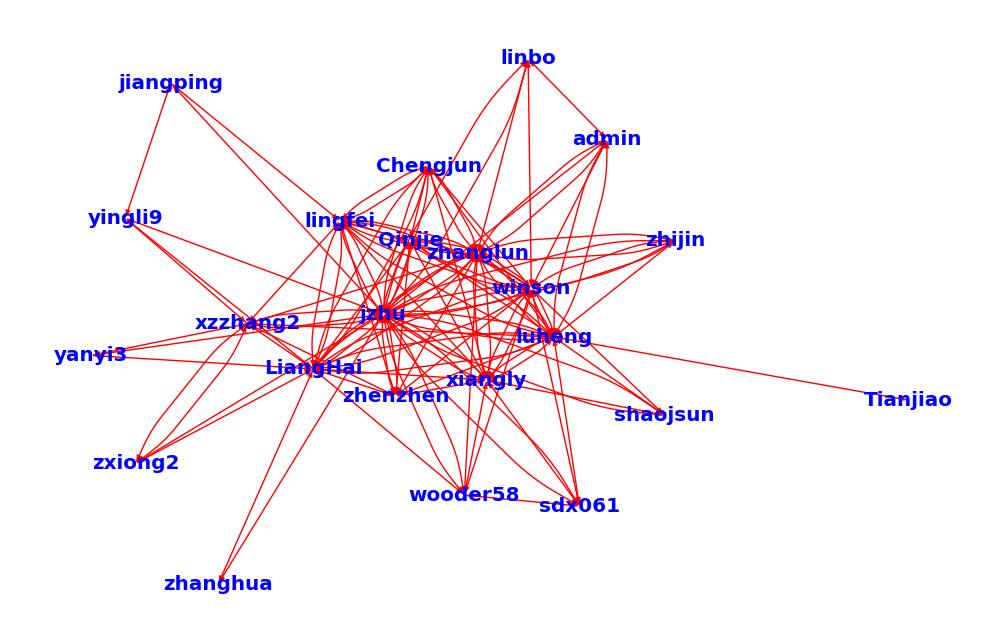

```mathematica
GraphPlot[Tally[bbs],ImageSize->1000,SelfLoopStyle->None,VertexLabeling->True,
EdgeRenderingFunction->({Red,Arrowheads[{-.01,.01}],Arrow[#1,0.01]}&),
VertexRenderingFunction->({Blue,Text[Style[#2,20,Bold],#1]}&)
]
```

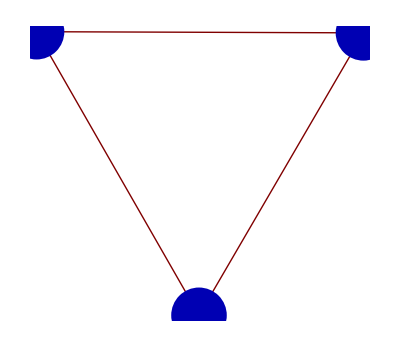

```mathematica
GraphPlot[{1->2,2->3,3->1},PlotStyle->{PointSize[0.1]}]
```

```mathematica
g={{"Owen"->"Monroe",2813},{"Greene"->"Monroe",3788},{"Lawrence"->"Monroe",4022},{"Jackson"->"Monroe",85},{"Brown"->"Monroe",689},{"Morgan"->"Monroe",821},{"Monroe"->"Owen",676},{"Monroe"->"Greene",207},{"Monroe"->"Lawrence",679},{"Monroe"->"Brown",303},{"Monroe"->"Morgan",617}};
```

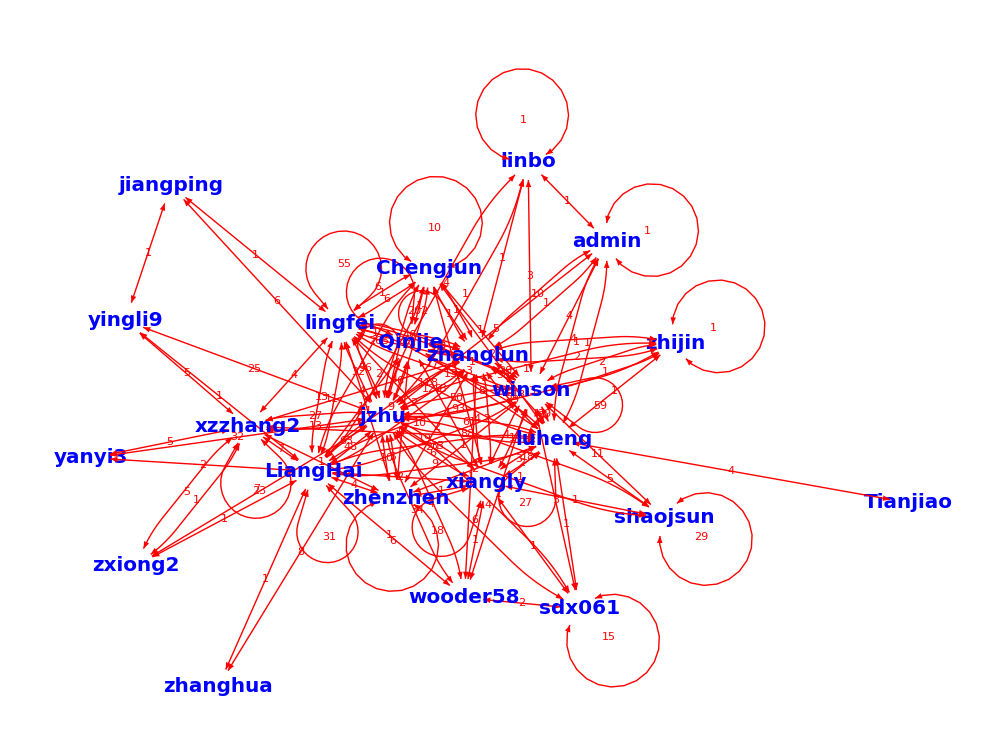

```mathematica
GraphPlot[Tally[bbs],VertexLabeling->True,ImageSize->1000,
EdgeRenderingFunction->({Red,Text[#3,Mean[#1]],Arrowheads[{-.01,.01}],Arrow[#1,0.1],Thickness[2]}&),
VertexRenderingFunction->({White,EdgeForm[Black],Blue,Text[Style[#2,20,Bold],#1]}&)]
```

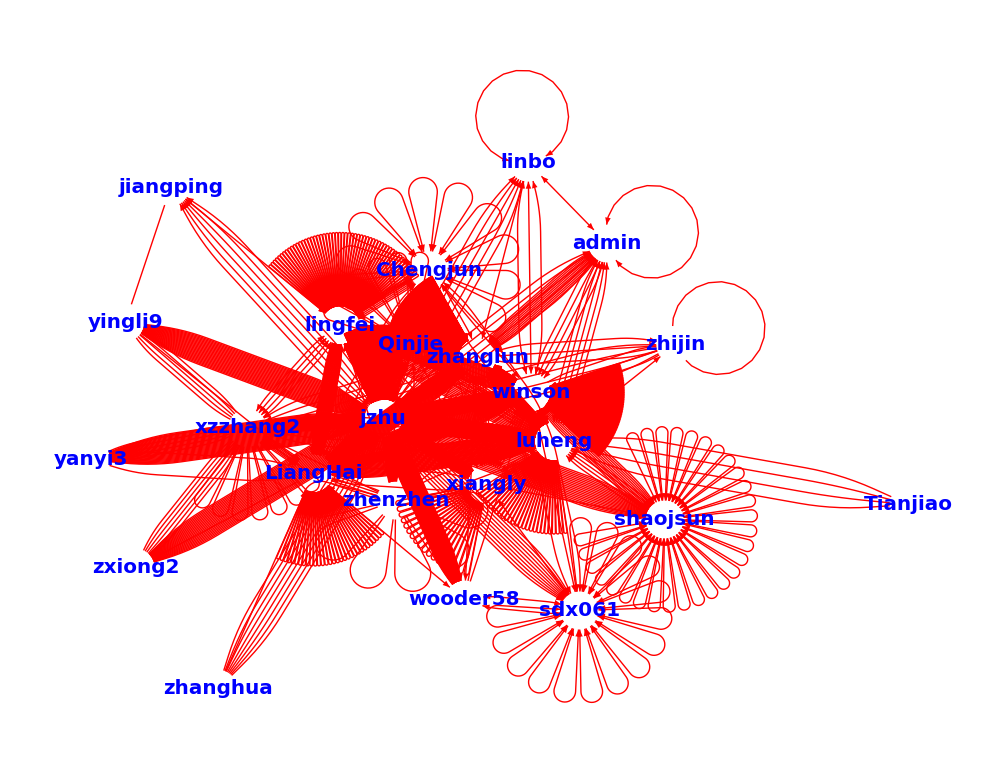

```mathematica
GraphPlot[bbs,VertexLabeling->True,ImageSize->1000,
EdgeRenderingFunction->({Red,Arrowheads[{-.01,.01}],Arrow[#1,0.1],Thickness[2]}&),
VertexRenderingFunction->({White,EdgeForm[Black],Blue,Text[Style[#2,20,Bold],#1]}&)]
```